# Motor Characterization Analysis

```mathematica
SetDirectory@NotebookDirectory[];
```

## Load and parse the data

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Import["test results 12-12-2016.txt","Elements"]
```

{Data,Lines,Plaintext,String,Words}

```mathematica
data=Import["test results 12-12-2016.txt","Lines"];
data=Cases[data,Except[""]][[2;;]];
data=Split[data,And[StringContainsQ[#1,"Current"],StringContainsQ[#2,"Current"]]&];
weights=StringSplit[#,"g"][[1]]&/@Flatten@data[[1;;;;2]];
data=data[[2;;;;2]];
parsed=Flatten@MapThread[Map[(result@@Prepend[ToExpression/@(StringSplit[#,","][[2;;;;2]]),weight]&)/.weight->ToExpression@#1,#2]&,{weights,data}];
```

```mathematica
"result[mass,power,current,speed]"
Column@parsed;
```

result[mass,power,current,speed]

### Convert the data to standard units

```mathematica
final=parsed;
final[[All,1]]=N@UnitConvert[(final[[All,1]]*Quantity[, "Grams"]+Quantity[5, "Grams"])*Quantity[, "StandardAccelerationOfGravity"]*Quantity[2.5, "Centimeters"],"Newton-Meters"];
final[[All,2]]=N@final[[All,2]]/255;
final[[All,3]]=final[[All,3]]*Quantity[5, "Volts"]/1023;
final[[All,4]]=final[[All,4]]/12*Quantity[, ("Revolutions")/("Seconds")];
```

```mathematica
"result[mass,power,current,speed]"
Column@final;
```

result[mass,power,current,speed]

## Plot and analyze the data

```mathematica
weightGroupings=SortBy[#,(#[[2]]&)]&/@GroupBy[final,#[[1]]&];
Column@weightGroupings;
```

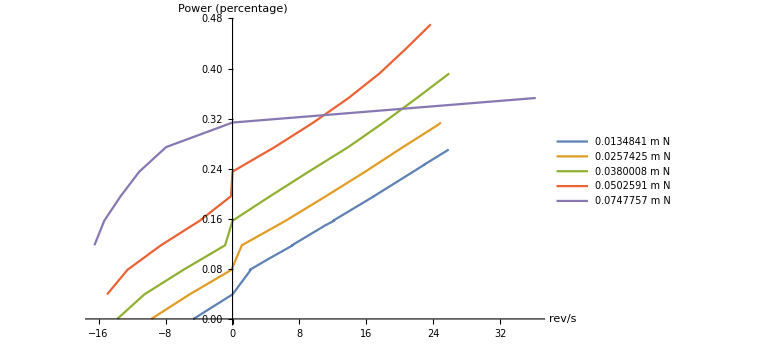

```mathematica
ListLinePlot[({#[[4]],#[[2]]}&/@#)&/@Values@weightGroupings,AxesLabel->{Automatic,"Power (percentage)"},PlotLegends->Keys@weightGroupings,ImageSize->Large]
```

## Guess the form of the key equation

```mathematica
ClearAll[power]
power[torque_,speed_]:=Module[{sol,deadzonespeed,deadzoneadjust},
sol=k1 (torque) -k2 speed;
deadzonespeed=Max[Min[k3,speed],-k3];
deadzoneadjust=k4 deadzonespeed;
sol+deadzoneadjust
]
```

## Fit the data

```mathematica
tspdata=QuantityMagnitude[List@@@final[[;;-2,{1,4,2}]]];
(*tspdata=Cases[tspdata,{_,_,speed_}/;Abs[speed]<10];*)
```

```mathematica
fit=FindFit[tspdata,power[t,s],{k1,k2,k3,k4},{t,s}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{k1→4.11622,k2→-0.00841818,k3→0.133333,k4→0.0876488}

```mathematica
fitted=Table[power[torque,speed],{torque,QuantityMagnitude@Keys@weightGroupings}]/.fit
```

{0.0555037+0.00841818 speed+0.0876488 Max[-0.133333,Min[0.133333,speed]],0.105962+0.00841818 speed+0.0876488 Max[-0.133333,Min[0.133333,speed]],0.156419+0.00841818 speed+0.0876488 Max[-0.133333,Min[0.133333,speed]],0.206877+0.00841818 speed+0.0876488 Max[-0.133333,Min[0.133333,speed]],0.307793+0.00841818 speed+0.0876488 Max[-0.133333,Min[0.133333,speed]]}

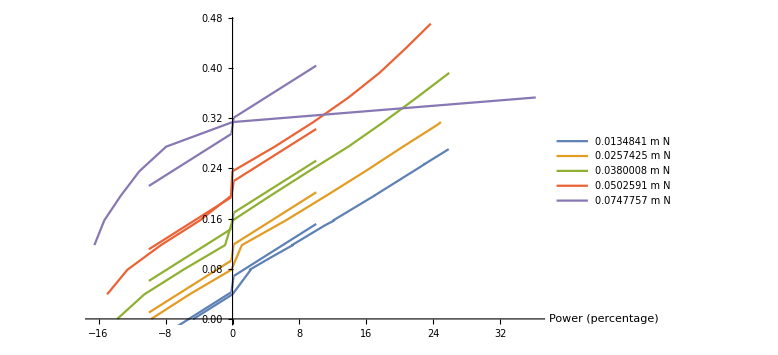

```mathematica
fitplot=Plot[fitted,{speed,-10,10}];
dataplot=ListLinePlot[({#[[4]],#[[2]]}&/@#)&/@Values@weightGroupings,AxesLabel->{"Power (percentage)",Automatic},PlotLegends->Keys@weightGroupings,ImageSize->Large];
Show[dataplot,fitplot]
```

```mathematica
CForm[ power[torque,speed]/.fit]/.{Min->min,Max->max}
```

0.008418180584179515*speed + 4.116216452954544*torque + 
   0.08764875554299961*max(-0.1333333250597091,min(0.1333333250597091,speed))